```mathematica
f[T_]:=2.192+9.240*10^(-4) T-1.41*10^(-7) T^2;
f2[T_]:=2.5+(Th^2/T^2) E^(-Th /T)/(1-E^(-Th /T))^2;
Th=3103
```

3103

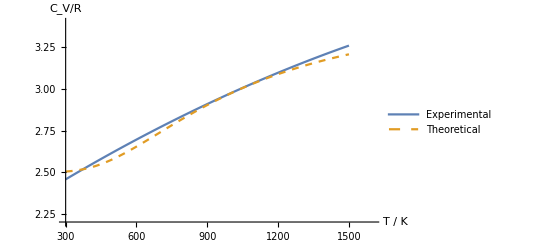

```mathematica
Plot[{f[T],f2[T]},{T,300,1500},PlotStyle->{Automatic,Dashed},PlotRange->{{300,1600},{2.2,3.4}},PlotLegends->Placed[{"Experimental","Theoretical"},{Scaled[{0.6,0.3}], {0, 0.5}}],AxesLabel->{"T / K","C_V/R"}]
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ProtonMass
```

1.67262×10^-27 Kilogram

```mathematica
PlanckConstant
```

6.62607×10^-34 Joule Second

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

```mathematica
T=3000;
Cv[Th_]:=(Th/T)^2 E^(-Th/T)/(1-E^(-Th/T))^2
```

```mathematica
N[5/2+Cv[3016]+2*Cv[1026]+Cv[4763]]
```

6.21447

```mathematica
T=1000;
Cv[Th_]:=(Th/T)^2 E^(-Th/T)/(1-E^(-Th/T))^2;
N[{Cv[1898],Cv[1078],Cv[2327]}]
```

{0.747014,0.908537,0.648903}

```mathematica
Total[{0.7470141336482113,0.9085371879988977,0.6489031068146788}]
```

2.30445

```mathematica
g[T_]:=1.099+7.27*10^(-3) T+1.34*10^(-7) T^2-8.67*10^(-10) T^3;
Cv2[T_,Th_]:=(Th/T)^2 E^(-Th/T)/(1-E^(-Th/T))^2;
g2[TT_]:=3+Total[{Cv2[TT,4170],2 Cv2[TT,2180],3 Cv2[TT,4320], 3 Cv2[TT,1870]}]
```

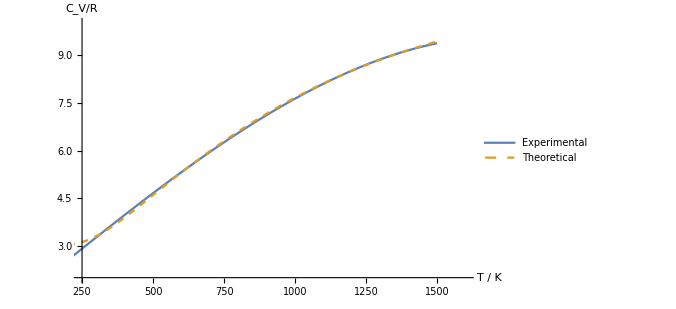

```mathematica
Plot[{g[TT],g2[TT]},{TT,200,1500},PlotStyle->{Automatic,Dashed},PlotRange->{{250,1600},{2,10}},PlotLegends->Placed[{"Experimental","Theoretical"},{Scaled[{0.7,0.3}], {0, 0.5}}],AxesLabel->{"T / K","C_V/R"}]
```

```mathematica
Integrate[E^(-J^2 a),{J,0,Infinity}]
```

ConditionalExpression[(√π)/(2 √a),Re[a]>0]